# Chapter 4 (R0, μ) Region Outcomes:

Define the necessary parameters :

```mathematica
m = 1.5;
```

```mathematica
c = 2;
ω = 1;
d = 1;
λ12 = 2;
λ21 = -3;
ι12 = -2;
ι21 = 1;
```

```mathematica
(*producing this region plot takes some time. to simulate it's easier to just select the values for parameters and run the code below*)
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

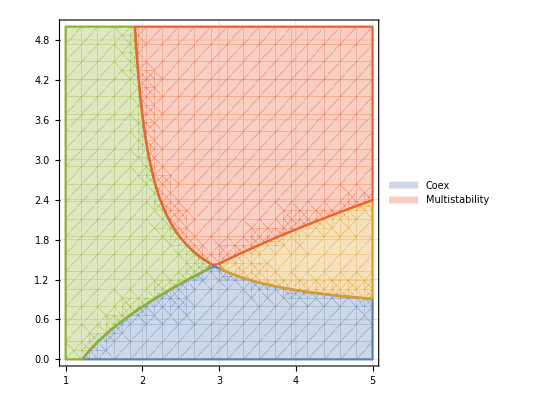

```mathematica
region = RegionPlot[{OutcomeFreeLambdas[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] == 0,
OutcomeFreeLambdas[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] == 1, OutcomeFreeLambdas[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] == 2, OutcomeFreeLambdas[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] == 3}, {R0,1 , 5}, {μ, 0, 5}, PlotTheme->"Detailed", FrameLabel->{"", ""}, PlotLegends->{"Coex ", "", "", "Multistability"}]
```

Now choose a point in :

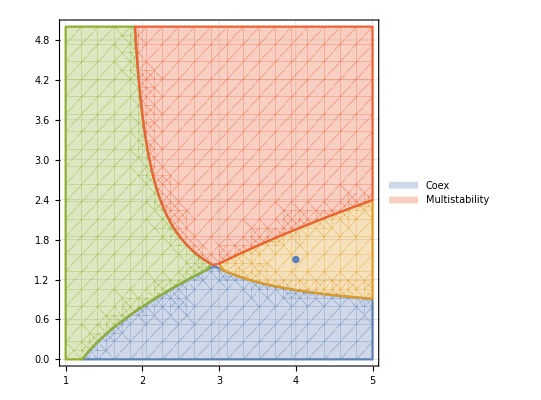

```mathematica
R0 = 4;
μ = 1.5;
Show[{region, ListPlot[{{R0, μ}}]}]
```

And some initial conditions:

```mathematica
(3, 3)
(2, 2),
(3, 1),
(4, 1.5)
```

```mathematica
zA0 = 0.8;
zB0 = 0.6;
```

Now simulate the system:

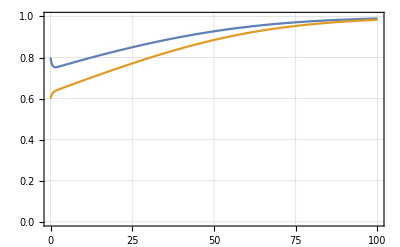

```mathematica
sol = FreeSolution[c, ω, R0, μ, d, λ12,λ21, ι12, ι21 , zA0, zB0];
Plot[{zA[t]/.sol, zB[t]/.sol}, {t, 0, 100}, PlotTheme->"Detailed", PlotLegends->{"", ""}, FrameLabel->{"", ""}, PlotRange->{0, 1}]
```

```mathematica
eq = FreeEquilibria[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] ;
StabilityReport[c, ω, R0, μ, d, λ12, λ21, ι12, ι21, eq]
```

({zA→1.,zB→1.} | True
{zA→0.304944,zB→0.262869} | False
{zA→0.,zB→0.} | True)

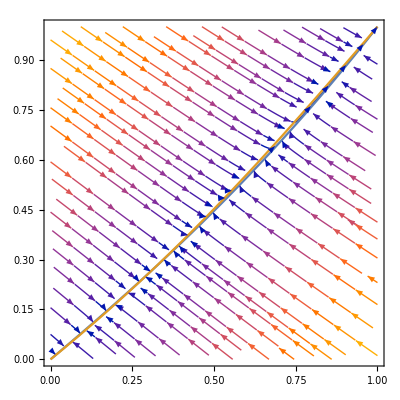

```mathematica
FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21]
```

```mathematica
Clear[d]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

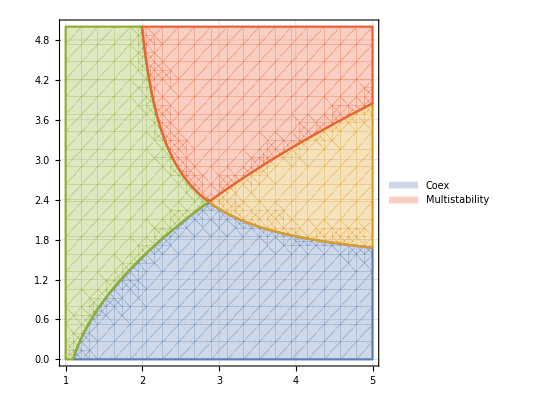
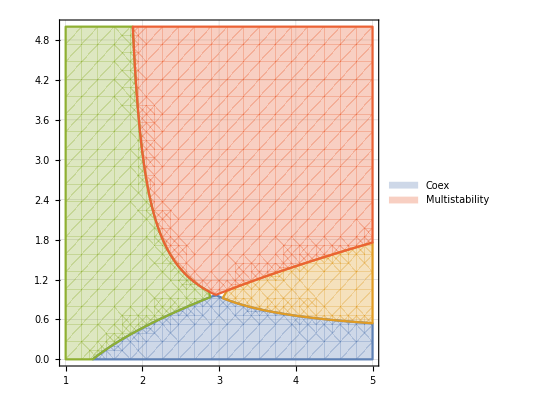
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
regionsD = Table[RegionPlot[{OutcomeFreeLambdas[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] == 0,
OutcomeFreeLambdas[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] == 1, OutcomeFreeLambdas[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] == 2, OutcomeFreeLambdas[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] == 3}, {R0,1 , 5}, {μ, 0, 5}, PlotTheme->"Detailed", FrameLabel->{"", ""}, PlotLegends->{"Coex ", "", "", "Multistability"}], {d, 0.5, 1.5, 0.5}]
```

```mathematica
regionsD[[3]]
```

-Graphics-

```mathematica
testRegion = FreeRegionRmuPlot[1, 5, 0, 5, c, ω, d, λ12, λ21, ι12, ι21]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.75+0.23059 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

-Graphics-

```mathematica
R0 = 3.2;
μ = 1.4;
```

```mathematica
Show[{testRegion, ListPlot[{{R0, μ}}]}]
```

-Graphics-

```mathematica
zA0 = 0.93;
zB0 =0.89;
```

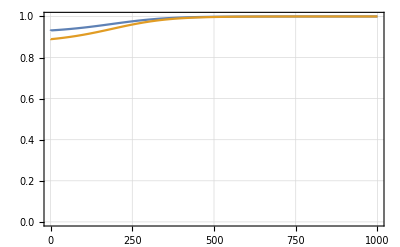

```mathematica
sol = FreeSolution[c, ω, R0, μ, d, λ12,λ21, ι12, ι21 , zA0, zB0];
Plot[{zA[t]/.sol, zB[t]/.sol}, {t, 0, 1000}, PlotTheme->"Detailed", PlotLegends->{"", ""}, FrameLabel->{"", ""}, PlotRange->{0, 1}]
```

```mathematica
eq = FreeEquilibria[c, ω, R0, μ, d, λ12, λ21, ι12, ι21] ;
StabilityReport[c, ω, R0, μ, d, λ12, λ21, ι12, ι21, eq]
```

({zA→1.,zB→1.} | True
{zA→0.920322,zB→0.871118} | False
{zA→0.416107,zB→0.281225} | True
{zA→0.,zB→0.} | False)

# Chapter 5: (ω, c) region outcomes

```mathematica
R0 = 1.2;
μ = 1;
d = 0.2;
m = 1.5;
```

(0.16 | 0.3
0.4 | 0.6)

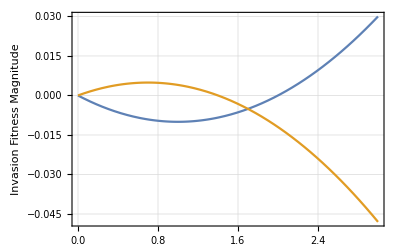

```mathematica
Alpha = {{0.16, .3},
		{.4, .6}};
Alpha // MatrixForm
Plot[{λ12[R0, μ, Alpha], λ21[R0, μ, Alpha]}, {μ, 0, 3}, PlotLegends->{"", ""},FrameLabel->{"", "Invasion Fitness Magnitude"}, PlotTheme->"Detailed"]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

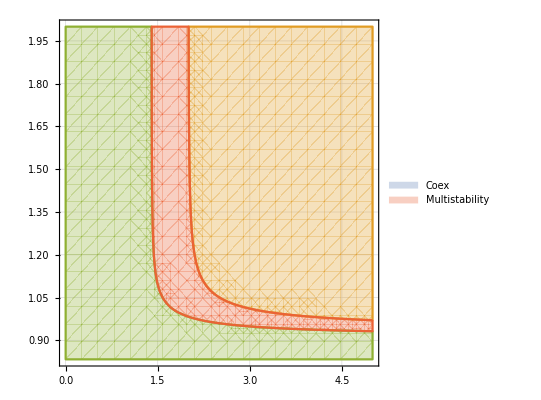

```mathematica
reg = RegionPlot[{Outcome[c, ω, R0, μ, d, Alpha] == 0,
Outcome[c, ω, R0, μ, d, Alpha] == 1, Outcome[c, ω, R0, μ, d, Alpha] == 2, Outcome[c, ω, R0, μ, d, Alpha] == 3}, {ω,0 , 5}, {c, 1/R0, 2}, PlotTheme->"Detailed", FrameLabel->{"", ""}, PlotLegends->{"Coex ", "", "", "Multistability"}]
```

now choose some c and ω

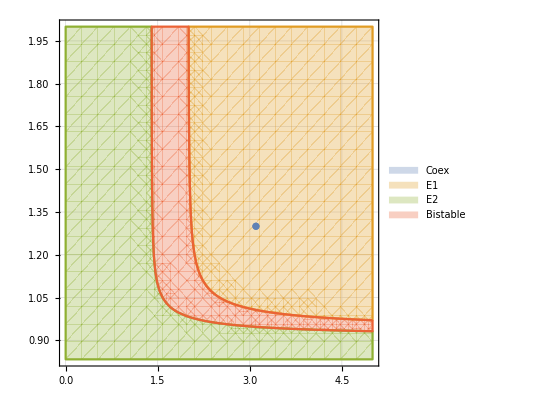

```mathematica
c = 1.3;
ω = 3.1;
Show[{reg, ListPlot[{{ω, c}}]}]
```

And some initial conditions:

```mathematica
zA0 = 0.8;
zB0 = 0.4;
```

Now simulate the system:

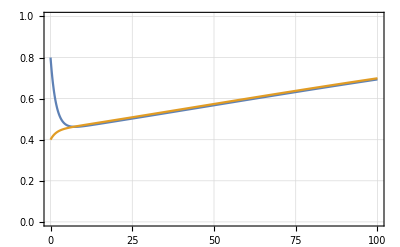

```mathematica
solution = Solution[c, ω, R0, μ, d, Alpha, zA0, zB0];
Plot[{zA[t]/.solution, zB[t]/.solution}, {t, 0, 100}, PlotTheme->"Detailed", PlotLegends->{"", ""}, FrameLabel->{"", ""}, PlotRange->{0, 1}]
```

```mathematica
equi = Equilibria[c, ω, R0, μ, d, Alpha] ;
StabilityReport[c, ω, R0, μ, d, λ12[R0, μ, Alpha], λ21[R0, μ, Alpha], λ12[c*R0, ω*μ, Alpha], λ21[c*R0, ω*μ, Alpha], equi]
```

({zA→1.,zB→1.} | True
{zA→0.,zB→0.} | False)